## Systems of nonlinear equations.

To start our investigation into systems of nonlinear equations, let's consider the pair of nonlinear equations:

	x^2+y^2=4
e^x+ y =1
	
If we viewed these equation graphically we and see that these equations intersect near the points (-1.8,0.8) and (1,-1.7).

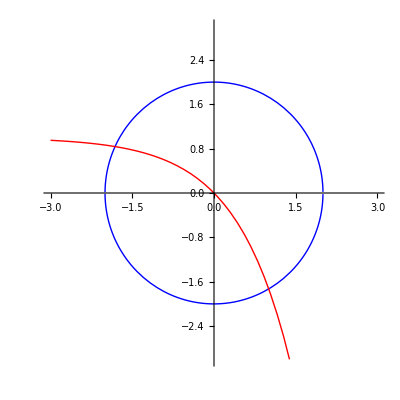

```mathematica
plot1=Plot[{Sqrt[4-x^2],-Sqrt[4-x^2],1-Exp[x]},{x,-3,3},AspectRatio->Automatic,PlotStyle->{{Thick,Blue},{Thick,Blue},{Thick,Red}},PlotRange->{{-3,3},{-3,3}}]
```

We could take a Gauss-Siedellike approach by rearranging the equations as follows:

	x=±√(4-y^2)
y=1-e^x
	
We can use an initial guess y_0 to find x_0, then x_0 to find y_1 and so on.

◀     |     ▶

## Gauss-Siedel-like iteration example.

If we do exactly as described previously we have the following using an initial guess of y_0=0.8.  (We are shooting for the leftmost root)

```mathematica
plot1=Plot[{Sqrt[4-x^2],-Sqrt[4-x^2],1-Exp[x]},{x,-3,3},AspectRatio->Automatic,PlotStyle->{{Thick,Blue},{Thick,Blue},{Thick,Red}},PlotRange->{{-3,3},{-3,3}}];
y=0.8;
x=0.0;
pointList={{x,y}};
points=Graphics[{PointSize[Large],Black,Point[{x,y}]}];
animatePlot={Show[plot1,points]};
Do[
x=-Sqrt[4-y^2];
y=1-E^x;
AppendTo[pointList,{x,y}];
points=Graphics[{PointSize[Large],Black,Point[{x,y}]}];
AppendTo[animatePlot,Show[plot1,points]];
,{6}];
ListAnimate[animatePlot,0.5]
```

It worked!  Let's now try an initial guess of  y_0=-1.7 and shoot for the rightmost root.

```mathematica
plot1=Plot[{Sqrt[4-x^2],-Sqrt[4-x^2],1-Exp[x]},{x,-3,3},AspectRatio->Automatic,PlotStyle->{{Thick,Blue},{Thick,Blue},{Thick,Red}},PlotRange->{{-3,3},{-3,3}}];
y=-1.7;
x=0.0;
pointList={{x,y}};
points=Graphics[{PointSize[Large],Black,Point[{x,y}]}];
animatePlot={Show[plot1,points]};
Do[
x=Sqrt[4-y^2];
y=1-E^x;
AppendTo[pointList,{x,y}];
points=Graphics[{PointSize[Large],Black,Point[{x,y}]}];
AppendTo[animatePlot,Show[plot1,points]];
,{6}];
ListAnimate[Take[animatePlot,4],0.5]
```

What happened?  Well, the method went unstable and ended up diverging into the imaginary plane.  The actual numbers are shown below.

```mathematica
ListAnimate[pointList]
```

However, if we simply rewrite the equations as follows:

	x=ln(1-y)
y=±√(4-x^2)
	
We can use the initial guess of y_0=-1.7 and it will converge to the solution.

```mathematica
plot1=Plot[{Sqrt[4-x^2],-Sqrt[4-x^2],1-Exp[x]},{x,-3,3},AspectRatio->Automatic,PlotStyle->{{Thick,Blue},{Thick,Blue},{Thick,Red}},PlotRange->{{-3,3},{-3,3}}];
y=-1.7;
x=0.0;
pointList={{x,y}};
points=Graphics[{PointSize[Large],Black,Point[{x,y}]}];
animatePlot={Show[plot1,points]};
Do[
x=Log[1-y];
y=-Sqrt[4-x^2];
AppendTo[pointList,{x,y}];
points=Graphics[{PointSize[Large],Black,Point[{x,y}]}];
AppendTo[animatePlot,Show[plot1,points]];
,{6}];
ListAnimate[animatePlot,0.5]
```

This simple example illustrates some of the difficulties that can arise when trying to solve systems of nonlinear equations.   Finding a convergent form of the equations gets increasingly difficult as the number of equations gets larger.

◀     |     ▶

## Newton's method for systems of nonlinear equations.

Consider the following systems of two nonlinear equations:

	f(x,y)=0
g(x,y)=0
	
Let x=r, y=s and  expand both functions as a Taylor series about the point (x_i,y_i) in terms of (r - x_i), (s-y_i), where (x_i,y_i) is a point near the root.  We have:

	f(r,s)=f(x_i,y_i)+f_x(x_i,y_i)(r-x_i)+f_y(x_i,y_i)(s-y_i)+…
g(r,s)=g(x_i,y_i)+g_x(x_i,y_i)(r-x_i)+g_y(x_i,y_i)(s-y_i)+…
	
If we keep only the linear terms we can write the equations in matrix form as:

	(0
0)=(f(x_i,y_i)
g(x_i,y_i))+(f_x(x_i,y_i) | f_y(x_i,y_i)
g_x(x_i,y_i) | g_y(x_i,y_i))(r-x_i
s-y_i)
	
or rearranging, we have:

	-(f(x_i,y_i)
g(x_i,y_i))=(f_x(x_i,y_i) | f_y(x_i,y_i)
g_x(x_i,y_i) | g_y(x_i,y_i))(Δ x_i
Δ y_i)
	
We can solve the equation above using Gaussian elimination for (Δ x_i,Δ y_i) then the next approximation becomes:

	x_(i+1)=x_i+Δ x_i
y_(i+1)=y_i+Δ y_i
	
This procedure generalized to n number of equations in a straightforward manner.

◀     |     ▶

## Newton's method example.

Using Newton's method to solve the same example as before, we can see that it will converge to either root with an appropriate guess.

```mathematica
x0=0.0;y0=-1.7;
```

```mathematica
x=.;y=.;
F={4-x^2-y^2,1-Exp[x]-y};
J=D[F,{{x,y}}];
Δ=LinearSolve[J,-F];
plot1=Plot[{Sqrt[4-x^2],-Sqrt[4-x^2],1-Exp[x]},{x,-3,3},AspectRatio->Automatic,PlotStyle->{{Thick,Blue},{Thick,Blue},{Thick,Red}},PlotRange->{{-3,3},{-3,3}}];
pointList={{x0,y0}};
points=Graphics[{PointSize[Large],Black,Point[{x0,y0}]}];
animatePlot={Show[plot1,points]};

Do[
x0+=(Δ[[1]]/.{x->x0,y->y0});
y0+=(Δ[[2]]/.{x->x0,y->y0});
AppendTo[pointList,{x0,y0}];
points=Graphics[{PointSize[Large],Black,Point[{x0,y0}]}];
AppendTo[animatePlot,Show[plot1,points]];
,{10}
];
ListAnimate[animatePlot]
```

```mathematica
x0=0.0;y0=0.8;
```

```mathematica
x=.;y=.;
F={4-x^2-y^2,1-Exp[x]-y};
J=D[F,{{x,y}}];
Δ=LinearSolve[J,-F];
plot1=Plot[{Sqrt[4-x^2],-Sqrt[4-x^2],1-Exp[x]},{x,-3,3},AspectRatio->Automatic,PlotStyle->{{Thick,Blue},{Thick,Blue},{Thick,Red}},PlotRange->{{-3,3},{-3,3}}];
pointList={{x0,y0}};
points=Graphics[{PointSize[Large],Black,Point[{x0,y0}]}];
animatePlot={Show[plot1,points]};

Do[
x0+=(Δ[[1]]/.{x->x0,y->y0});
y0+=(Δ[[2]]/.{x->x0,y->y0});
AppendTo[pointList,{x0,y0}];
points=Graphics[{PointSize[Large],Black,Point[{x0,y0}]}];
AppendTo[animatePlot,Show[plot1,points]];
,{10}
];
ListAnimate[animatePlot]
```

◀     |     ▶

## Pseudocode for Newton's method for systems.

To approximate the solution of the nonlinear system F(x̄)=0.  Given an initial guess vector x̄={x_1,x_2,...,x_n}^T

Step 1.  Set k=1

Step 2.  While k< max iteration and ERR > TOL then do Steps 3-7

	Step 3.  Calculate F(x̄) and J(x̄), where (J(x̄))_(i j)=∂/(∂x_j)f_i(x̄)
	Step 4.  Solve the linearized equation J(x̄)Δ x̄=-F(x̄)
	
	Step 5.  Set x̄=x+Δ x̄
	
	Step 6.  ERR = ||Δ x̄||
	
	Step 7.  k=k+1

◀     |     ▶

## Quasi-Newton methods.

A significant weakness of Newton's method for solving systems of nonlinear equations is that, for each iteration, a Jacobian matrix has to be computed and an n × n linear system solved.  Let's consider the number of computations associated with one iteration of Newton's method.  The Jacobian matrix associated with a system of n nonlinear equations written in the form F(x)=0 requires that the n^2 partial derivatives of the n component functions of F to be determined and evaluated.  When the exact evaluation of the partial derivatives is not easily accomplished we can use  a finite difference approximation to the partial derivatives, for example:

	(∂f_j)/(∂x_k)(x̄)≈(f_j(x̄+(ē)_k h)-f_i(x̄))/h
	
where h is small in absolute value and (ē)_k is the vector whose only nonzero entry is a 1 in the k^th coordinate.  This approximation still requires that at least n^2 scalar functional evaluations be performed to approximate the Jacobian matrix, there doesn't increase the efficiency of the computation.  

There are a class of methods known as least-change secant updates that produce algorithms called quasi-Newton.  These methods replace the Jacobian matrix in Newton's method with an approximation matrix that is updated at each iteration.  We lose the quadratic convergence of Newton's method with these techniques, but in general they are still superlinear.  One of these quasi-Newton methods we will consider is called Broyden's method.

◀     |     ▶

## Broyden's Method

Suppose we have an initial approximation (x̄)^(0) to the solution of a system of nonlinear equations F(x)=0.  We calculate the next approximations (x̄)^(1) in exactly the same fashion as Newton's method, or in the case where the Jacobian matrix is difficult to explicitly evaluate we can use the finite difference approximation described on the previous slide.  To compute (x̄)^(2) we depart from Newton's method and examine the Secant method for a single nonlinear equation.  The Secant method uses the approximation:

	f'(x)≈(f(x_1)-f(x_0))/(x_1-x_0)
	
For nonlinear systems (x̄)^(1)-(x̄)^(0) is a vector, and the corresponding quotient is undefined.  However, the method proceeds similarly in that we replace the matrix J((x̄)^(1)) in Newton's method for systems by a matrix A_1 with the property that:

	A_1((x̄)^(1)-(x̄)^(0))=F((x̄)^(1))-F((x̄)^(0)) (*)
	
Any nonzero vector in ℝ^n can be written as the sum of a multiple of (x̄)^(1)-(x̄)^(0) and a multiple of a vector in the orthogonal complement of (x̄)^(1)-(x̄)^(0).  So to uniquely define the matrix A_1, we need to specify how it acts on the orthogonal complement of (x̄)^(1)-(x̄)^(0).  There is no information available about the change in F in a direction orthogonal to (x̄)^(1)-(x̄)^(0),  therefore we require that:

	A_1 z̄=J((x̄)^(0))z̄, 	whenever ((x̄)^(1)-(x̄)^(0))^T z̄=0 (**)
	
Thus, any vector orthogonal to (x̄)^(1)-x^(0) is unaffected by the update from J((x̄)^(0)), which was used to compute (x̄)^(1), to A_1, which is used in the determination of (x̄)^(2).   Conditions (*) and (**) uniquely define A_1 as:

	A_1=J((x̄)^(0))+([F((x̄)^(1))-F((x̄)^(0))-J((x̄)^(0))((x̄)^(1)-(x̄)^(0))]((x̄)^(1)-(x̄)^(0))^T)/(||(x̄)^(1)-(x̄)^(0)(||)^2) (***)
	
A_1 is then used in place of J((x̄)^(1))  to determine (x̄)^(2) as

	(x̄)^(2)=(x̄)^(1)-A_1^-1 F((x̄)^(1))
	
For (x̄)^(3) we replace use J((x̄)^(0)) with A_1.  So in general we have:

	A_i=A_(i-1)+((ȳ)_i-A_(i-1)(s̄)_i)/(||(s̄)_i(||)^2)s_i^T	and 	(x̄)^(i+1)=(x̄)^(i)-A_i^-1(F((x̄)^(i)))_
	
where (s̄)_i=(x̄)^(i)-(x̄)^(i-1) and (ȳ)_i=F((x̄)^(i))-F((x̄)^(i-1)).

If the method is employed as outlined above the number of scalar functional evaluations is reduced from n^2+n to n, but there still O(n^3) computations required to solve the linear system:

	A_i s_(i+1)=-F((x̄)^(i))
	
Left alone, this would not justify it's use because of the reduction from quadratic to superlinear convergence as opposed to just using Newton's method.  We will see that we will greatly improve this method with the use of the Sherman-Morrison formula.

◀     |     ▶

## Sherman-Morrison Formula.

The Sherman-Morrison formula states the following:

If A is a nonsingular matrix and x̄ and ȳ are vectors, the A+x̄(ȳ)^Tis nonsingular, provided that (ȳ)^T A^-1 x̄≠-1, and

	(A+x̄(ȳ)^T)^-1=A^-1-(A^-1 x̄(ȳ)^T A^-1)/(1+y^T A^-1 x̄)s_i^T
	
This permits A_i^-1 to be computed directly from A_(i-1)^-1 bypassing the need for matrix inversion after the first iteration.  Let's take a look at what happens when we apply the Sherman-Morrison formula to the general statement for solving for A_i in Broyden's method.

	A_i^-1=(A_(i-1)+((ȳ)_i-A_(i-1)(s̄)_i)/(||(s̄)_i(||)^2)s_i^T)^-1
          =A_(i-1)^-1-(A_(i-1)^-1(((ȳ)_i-A_(i-1)(s̄)_i)/(||(s̄)_i(||)^2)s_i^T)A_(i-1)^-1)/(1+(s̄)_i^T A_(i-1)^-1(((ȳ)_i-A_(i-1)(s̄)_i)/(||(s̄)_i(||)^2)s_i^T))
           =A_(i-1)^-1-((A_(i-1)^-1 y_i-(s̄)_i)s_i^T A_(i-1)^-1)/(||(s̄)_i(||)^2+(s̄)_i^T A_(i-1)^-1(ȳ)_i-||(s̄)_i(||)^2)
           =A_(i-1)^-1+(((s̄)_i-A_(i-1)^-1(ȳ)_i)(s̄)_i^T A_(i-1)^-1)/((s̄)_i^T A_(i-1)^-1(ȳ)_i)
	
This computation involves only matrix-vector multiplication at each step and therefore requires only O(n^2) arithmetic calculations.  We can bypass the calculation of A_i and the necessity of solving the linear system, greatly speeding up the  Broyden's method.

◀     |     ▶

## Pseudocode for Broyden's method.

To approximate the solution of the nonlinear system F(x)=0, given an initial guess x̄=(x_1,x_2,…,x_n)^T

Step 1.  Set A_0=J(x), where (J(x̄))_(i j)=∂/(∂x_j)f_i(x̄)
Step 2.  Set v̄=F(x̄)
Step 3.  Set  A=A_0^-1 	(must solve for A_0^-1)
Step 4.  Set s̄ = -A v̄
Step 5.  Set x̄=x̄+s̄
Step 6.  Set k=2

Step 7.  While k< max iterations do Steps 7-18

	Step 8.  Set w̄=v̄
	Step 9.  Set v̄=F(x̄)
	Step 10.  Set ȳ=v̄-w̄
	Step 11.  Set z̄=-A ȳ
	Step 12.  Set p=-(s̄)^T z̄
	Step 13.  Set (ū)^T=(s̄)^T A
	Step 14.  Set A=A+1/p(s̄+z̄)(ū)^T
	Step 15.  Set s̄=-A v̄
	Step 16.  Set x̄=x̄+s̄
	
	Step 17.  If ||s̄|| < TOL, stop program and output x̄
	Step 18.  Set k=k+1

◀     |     ▶

## Steepest Descent Techniques

We've already discussed the advantages of the fast convergence rates of Newton's method and quasi-Newton's methods, but a weakness of these methods for solving systems of nonlinear equations is the same problem that arises in single variable non-linear equations in that a close approximation to the solution is necessary for these methods to converge.  The Steepest Descent Technique presented here only converges linearly to the solution, but will usually converge even with a poor approximation.  Therefore is often used, much like the Bisection method for single variables, in order to get a good approximation to a root, before handing the algorithm off to one of the other methods in order to "polish off" the solution.  The Steepest Descent Technique is an optimization technique that determines the local minimum for a multivariable function of the form g: ℝ^n→ ℝ.  The method has uses outside of solving nonlinear systems of equations.  Consider the system of equations:

	f_1(x_1,x_2,…,x_n)=0
f_2(x_1,x_2,…,x_n)=0
                                            
f_n(x_1,x_2,…,x_n)=0
	
These equations have a solution x̄=(x_1,x_2,…,x_n)^T exactly when the function g defined by

	g(x_1,x_2,…,x_n)=∑_(i=1)^n [f_i(x_1,x_2,…,x_n)]^2
	
has a minimum value 0.  We know from calculus and the Extreme Value Theorem that a differentiable single-variable function can have a local minimum only when the derivative of that function is zero.  We can extend this to multivariable functions by considering the gradient:

	∇g(x)=((∂g(x))/(∂x_1),(∂g(x))/(∂x_2),...,(∂g(x))/(∂x_n))^T
	
A differentiable multivariable function can have a local minimum at x̄ only when ∇g(x̄)=0.  The gradient has another important property associated with the minimization of multivariable functions.  Let v̄=(v_1,v_2,…,(v̄)_n)^T be a unit vector in ℝ^n; that is:

	||v̄(||)^2=∑_(i=1)^n v_i^2=1
	
The directional derivative of g at x̄ in the direction of v̄ is defined by

	D_(v̄)g(x̄)=lim_(h→ 0) 1/h[g(x̄+h v̄)-g(x̄)]=(v̄)^T·∇g(x̄)
	
The directional derivative of g at x̄ in the direction of v̄ measures the change in the value of the function g relative to the change in the direction of v̄.  It turns out that the direction that produces the maximum value for the directional derivative (the fastest change in g) occurs when v̄ is chosen to be parallel with ∇g(x̄).  So if we are going to devise an iterative technique that minimized g we want to move at each step in the direction of -∇g(x̄) in order to get to 0 the fastest.  Therefore an appropriate choice for (x̄)^(1) given an initial guess (x̄)^(0) is:

	(x̄)^(1)=((x̄)^(0)-α ∇g( (x̄)^(0)))^.
	
where α represents the magnitude of distance we want to move in one step.  We want to choose an α that produces a g((x̄)^(1)) that is as far as possible from g((x̄)^(0)).  Another way of stating this is saying that we wish to now minimize the single variable equation:

	h(α)=g((x̄)^(0)-α ∇g((x̄)^(0)))
	
Finding  a minimal value for h directly would require differentiating h and then solving a root-finding problem to determine the critical points of h.  This procedure is too computationally expensive, instead, we choose three numbers α_1<α_2<α_3 that, we hope, are close to the minimum of h(α).  Then we construct the quadratic polynomial P(x) that interpolates h at α_1,α_2,α_3.  We define α̂ in [α_1,α_3] so that P(α̂) is a minimum in the interval and use P(α̂) to approximate the minimum (this will be close enough to the maximum distance between  g((x̄)^(1)) and g((x̄)^(0))).  Then we use α̂ to determine the new iterate.

	(x̄)^(1)=((x̄)^(0)-α̂ ∇g( (x̄)^(0)))^
	
Since g( (x̄)^(0)) can be evaluated, we can first chose α_1=0 to minimize h.  Next a number α_3 is found with h(α_3)<h(a_1).  Finally, α_2 is chosen to be α_3/2.  The minimum value of P on the interval will always occur at the only critical point of P or at α_3 because, by assumption, P(α_3)=h(α_3)<h(α_1)=P(α_1).   The critical point of P is easy to find since P is a quadratic polynomial.

◀     |     ▶

## Pseudocode for Steepest Decent Technique

To approximate a solution p̄ to the minimization problem:

	g(p̄)=min_(x̄∈ℝ^n) g(x̄)
	
given an initial approximation x̄

Step 1.  Set k=1
Step 2.  While k < max iterations do Steps 3-25

	Step 3.  Set g_1=g(x_1,x_2,…,x_n)
	Step 4.  Set z̄=∇g(x_1,x_2, …, x_n)
	Step 5.  Set z_0=||z̄||
	
	Step 6.  If z_0=0 then stop program and output "Zero gradient" and (x̄,g_1)
	
	Step 7.  Set z̄=z̄/z_0
	Step 8.  Set α_1=0
	Step 9.  Set α_3=1
	Step 10.  Set g_3=g(x̄-α_3 z̄)
	
	Step 11.  While (g_3≥ g_1) do Steps 12-14
	
		Step 12.  Set α_3=α_3/2
		Step 13.  Set g_3=g(x̄-α_3 z̄)
		
		Step 14.  If α_2<TOL/2 then stop program and output "No improvement likely" and (x̄,g_1)
		
	Step 15.  Set α_2=α_3/2
	Step 16.  Set g_2=g(x̄-α_2 z̄)
	
	Step 17.  Set h_1=(g_2-g_1)/α_2
	Step 18.  Set h_2=(g_3-g_2)/(α_3-α_2)
	Step 19.  Set h_3=(h_2-h_1)/α_3	(Here we are using Newton's forward divided-difference formula to find P that interpolates h)
	
	Step 20.  Set α_0=0.5(α_2-h_1/h_3)  	(This is the critical point of P)
	Step 21.  Set g_0=g(x̄-α_0 z̄)
	
	Step 22.  Find α from {α_0,α_3} so that g=g(x̄-α z̄)=min{g_0,g_3}
	
	Step 23.  Set x̄=x̄-α z̄
	
	Step 24.  If |g-g_1|<TOL then stop program and output (x̄,g)
	
	Step 25.  Set k=k+1

◀     |     ▶

## Survey of software for use in nonlinear root solving

The opensource subroutines for nonlinear root solving are somewhat more fragmented than those for linear systems of equations.  There are a few common ones you may look to in the IMSL and NAG libraries or MINPACK.  Of course MATLAB and Mathematica have powerful tools for us to use as well..

MINPACK | MATLAB | Mathematica
  | roots | NSolve
HYBRD,HYBRDJ | fzero | FindRoot

◀     |     ▶